```mathematica
Remove["Global`*"]
```

```mathematica
NotebookDirectory[]
```

/home/igor/Igor/proga/test/

```mathematica
Print["ptint a middle concentration"];
Directory[]
Remove["Global`*"]
zi= 0.42019;
read = 1;
time=15
nx=220;dx=4/nx;
nz=100;dz=2/nz;
path=NotebookDirectory[]<>"data/my/"<>ToString[time]<>"/"
exportPictures = path<>"pictures/"
CreateDirectory[exportPictures]
ColorBar= Table[{RGBColor[0.17954424800000002,0.303273768,0.937097728],RGBColor[0.26262173600000005,0.429350376,0.942562096],RGBColor[0.488318904,0.7191468160000001,0.961116924],RGBColor[0.6454961680000001,0.8671530960000001,0.975616328],RGBColor[0.7887495880000001,0.959560608,0.9869243600000001],RGBColor[0.88444604,0.99548318,0.96889742],RGBColor[0.988305752,0.994878884,0.837229796],RGBColor[0.983248968,0.950437888,0.6713337679999999],RGBColor[0.9508367280000001,0.843639316,0.514016],RGBColor[0.90055118,0.6453121999999999,0.33018259999999994],RGBColor[0.859578384,0.44239920000000005,0.225542096]}];
(*ContourBar= Table[{10,17,25,40,50,55,59,115,165,290,415}];*)
ContourBar= Table[{0.2,0.4,0.6,0.8,0.9,1,1.1,1.2,1.4,1.6}];
ContourBar2= Flatten[{0,ContourBar}];
nstart =2490;
ntdata =2490;
For[i=2,i<nz+1,i++
	For[ii=0,ii<nx+1,ii++,
	      nv[ii,i] = 0
	]
]
Monitor[
For[t=nstart,t≤ntdata ,t++,
If[read == 1,
If[t<10,
fnamedatad = path<>"all_concentr/all_concentr000"<>ToString[t]<>".dat";
];
If[t>9,If[t<100,
fnamedatad = path<>"all_concentr/all_concentr00"<>ToString[t]<>".dat";
];
];
If[t>99,If[t<1000,
fnamedatad = path<>"all_concentr/all_concentr0"<>ToString[t]<>".dat";
];
];
If[t>999,If[t<10000,
fnamedatad = path<>"all_concentr/all_concentr"<>ToString[t]<>".dat";
];
];
Data=ReadList[fnamedatad,{
Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number(*,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number*)}];
]

(*If[read == 0,
If[t<10,
fnamedatad = path<>"pict/data/data_concentration_"<>ToString[t]<>"_"<>ToString[np]<>".dat"
];
If[t>9,If[t<100,
fnamedatad = path<>"pict/data/data_concentration_"<>ToString[t]<>"_"<>ToString[np]<>".dat"
];
];
If[t>99,If[t<1000,
fnamedatad = path<>"pict/data/data_concentration_"<>ToString[t]<>"_"<>ToString[np]<>".dat"
];
];
If[t>999,If[t<10000,
fnamedatad = path<>"pict/data/data_concentration_"<>ToString[t]<>"_"<>ToString[np]<>".dat"
];
];
Data=ReadList[fnamedatad,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
]
*)
For[i=2,i<nz+1,i++
	For[ii=0,ii<nx+1,ii++, 
		nv[ii,i]=Data[[i]][[ii]];
	]
];
If[Mod[t,10]==0,
(*ColorBar= Table[{White,Yellow,Green,Blue,Pink,Red,Purple}];
ContourBar= Table[{1,100,200,300,500,1000}];
ContourBar2= Flatten[{0,ContourBar}];
(*fdata=Flatten[Table[{{x*dx,z*dz},nv[x,z]},{x,0,nx},{z,0,nz}],1];
f=Interpolation[fdata,InterpolationOrder->0];*)
datab=Flatten[Table[{x*dx,z*dz,nv[x,z]},{x,0,nx},{z,0,nz}],1];
GR = GraphicsRow[{
ListContourPlot[datab,Contours->ContourBar,ContourStyle->Black,PlotRange->{{0,3},{0,1.5},All},ClippingStyle->Green,RegionFunction->Function[{x,y,z},Abs[z]>0],BoundaryStyle->None,InterpolationOrder->3,ContourShading->{White,Yellow,Green,Blue,Pink,Red,Purple},ImageSize->400],Graphics[{EdgeForm[Gray],Table[{ColorBar[[t]],Text[Style[ContourBar2[[t]],Black],{1.5,t},{0,0},{1,0}],Rectangle[{0,t-0.5},{1,t+0.5}]},{t,1,7}]}]
}];*)

(*fdata=Flatten[Table[{{x*dx,z*dz},nv[x,z]},{x,0,nx},{z,0,nz}],1];
f=Interpolation[fdata,InterpolationOrder->0];*)
datab=Flatten[Table[{x*dx,z*dz,1.55*nv[x,z]},{x,0,nx},{z,2,nz}],1];
GR = GraphicsRow[{
ListContourPlot[datab,
AspectRatio->0.69,
Contours->ContourBar,
ContourLabels->Automatic,
ContourStyle->Black,
PlotRange->{{0,4},{0,1.2},All},
ClippingStyle->Green,
RegionFunction->Function[{x,y,z},Abs[z]>0],
BoundaryStyle->None,
InterpolationOrder->5,
ContourShading->{RGBColor[0.17954424800000002,0.303273768,0.937097728],RGBColor[0.26262173600000005,0.429350376,0.942562096],RGBColor[0.488318904,0.7191468160000001,0.961116924],RGBColor[0.6454961680000001,0.8671530960000001,0.975616328],RGBColor[0.7887495880000001,0.959560608,0.9869243600000001],RGBColor[0.88444604,0.99548318,0.96889742],RGBColor[0.988305752,0.994878884,0.837229796],RGBColor[0.983248968,0.950437888,0.6713337679999999],RGBColor[0.9508367280000001,0.843639316,0.514016],RGBColor[0.90055118,0.6453121999999999,0.33018259999999994],RGBColor[0.859578384,0.44239920000000005,0.225542096],RGBColor[0.847062048,0.37863690000000005,0.19544901199999998]},
ImageSize->500],Graphics[{EdgeForm[Gray],Table[{ColorBar[[t]],Text[Style[ContourBar2[[t]],Black],{1.5,t},{0,0},{1,0}],Rectangle[{0,t-0.5},{1,t+0.5}]},{t,1,11}]}]
}];
NameMovie = exportPictures<>"all_concentration_"<>ToString[t]<>".png";
Export[NameMovie,GR];
]
]
,t]
```

ptint a middle concentration

/home/igor

15

/home/igor/Igor/proga/fullDistribution/data/my/15/

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/

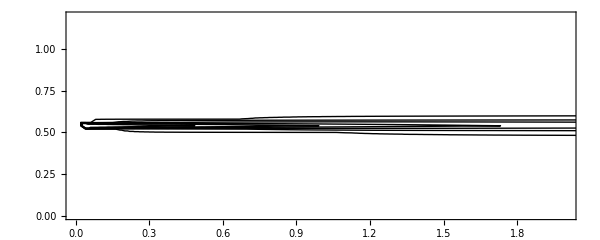

```mathematica
ContourBar= Table[{0.2,0.4,0.6,0.8,0.9,1,1.1,1.2,1.4,1.6,2,3,4,6}];
ContourBar= Table[{0.2,6.4,15.6,28.8,40.9,40.9,40.9,40.9,40.9,40.9,40.9,40.9,40.9,60}];
ContourBar2= Flatten[{0,ContourBar}];
datab=Flatten[Table[{1.1*x*dx,z*dz,1.62*nv[x,z]},{x,0,nx},{z,2,nz}],1];
GR=Show[
ListContourPlot[
datab,
AspectRatio->0.4,
Contours->ContourBar,
ContourLabels->Automatic,
ContourStyle->Black,
PlotRange->{{0,2},{0,1.2},All},
ClippingStyle->Green,
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->None,
ImageSize->600],
Graphics[{White,Rectangle[{3.95,0},{5,10}]}]
]
NameMovie = exportPictures<>"baw_all_concentration_"<>ToString[t]<>".png";
Export[NameMovie,GR];
```

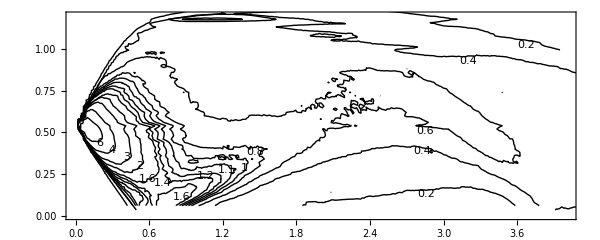

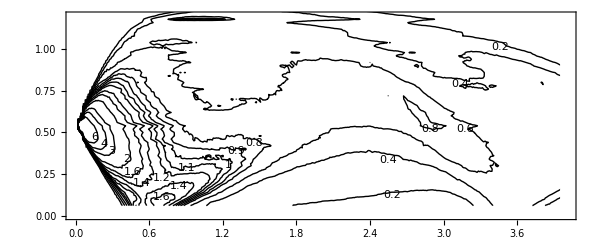

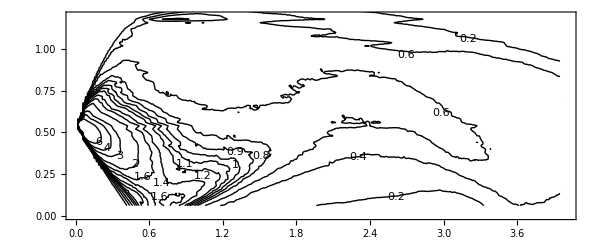

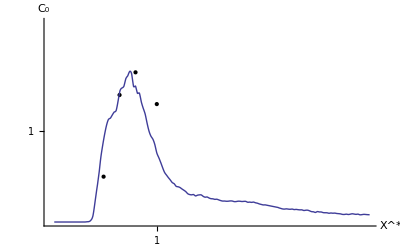

```mathematica
datab=Flatten[Table[{x*dx,1.55*nv[x,3]},{x,0,nx}],1];
data1=Table[{x*dx,1.55*nv[x,3]},{x,0,nx}];
Interpolation[%];
plot1=Plot[%[x],{x,0,3}];

points={{0.5,0.5},{0.65,1.4},{0.8,1.65},{1,1.3}};
GR2=Show[
ListPlot[points,PlotRange->{{0,3},{0,2.2}},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"X^*","C_0"},Ticks->{{1},{1}}],
plot1
]
NameMovie = exportPictures<>"earth.png";
Export[NameMovie,GR2];
```

```mathematica
datab=Flatten[Table[{x*dx,z*dz,1.55*nv[x,z]},{x,0,nx},{z,2,nz}],1];
(*ColorBar= Table[{RGBColor[0.185158312,0.311943504,0.933855864],RGBColor[0.25370274400000004,0.383988048,0.937759368],RGBColor[0.323781488,0.454864984,0.941852048],RGBColor[0.40705496,0.52699228,0.94715816],RGBColor[0.501712496,0.606351832,0.953915792],RGBColor[0.6551480000000001,0.7305258640000001,0.9662626879999999],RGBColor[0.7830380000000001,0.8304345040000001,0.979009568],RGBColor[0.89033872,0.915395944,0.989402496],RGBColor[0.956260032,0.966899384,0.9589245359999999],RGBColor[0.98632128,0.988611512,0.8763553199999999],RGBColor[0.99270912,0.991253048,0.7704922799999999],RGBColor[0.993525672,0.988560392,0.5366875359999999],RGBColor[0.977887,0.9370697999999998,0.3685955999999998],RGBColor[0.939821368,0.7991188079999999,0.270437064],RGBColor[0.9027606960000001,0.6513408560000001,0.24057348000000003],RGBColor[0.8675693999999999,0.4915453999999999,0.21120899999999998],RGBColor[0.8409845359999999,0.3160306799999997,0.18688014399999994],RGBColor[0.819291128,0.14928564,0.166106512]}];*)
ColorBar= Table[{RGBColor[0.185158312,0.311943504,0.933855864],RGBColor[0.25370274400000004,0.383988048,0.937759368],RGBColor[0.323781488,0.454864984,0.941852048],RGBColor[0.40705496,0.52699228,0.94715816],RGBColor[0.501712496,0.606351832,0.953915792],RGBColor[0.6551480000000001,0.7305258640000001,0.9662626879999999],RGBColor[0.7830380000000001,0.8304345040000001,0.979009568],RGBColor[0.89033872,0.915395944,0.989402496],RGBColor[0.956260032,0.966899384,0.9589245359999999],RGBColor[0.98632128,0.988611512,0.8763553199999999],RGBColor[0.99270912,0.991253048,0.7704922799999999],RGBColor[0.993525672,0.988560392,0.5366875359999999],RGBColor[0.977887,0.9370697999999998,0.3685955999999998],RGBColor[0.939821368,0.7991188079999999,0.270437064],RGBColor[0.9027606960000001,0.6513408560000001,0.24057348000000003],RGBColor[0.8675693999999999,0.4915453999999999,0.21120899999999998],RGBColor[0.8409845359999999,0.3160306799999997,0.18688014399999994],RGBColor[0.819291128,0.14928564,0.166106512]}];
ContourBar= Table[{0.2,0.4,0.6,0.8,0.9,1,1.1,1.2,1.4,1.6,2,3,4,6}];
ContourBar2= Flatten[{0,ContourBar}];
ContourBar2= Flatten[{0,ContourBar}];
GR = 
ListContourPlot[datab,
AspectRatio->0.3,
Contours->ContourBar,
ContourLabels->Automatic,
ContourStyle->Black,
PlotRange->{{0,4},{0,1.2},All},
ClippingStyle->Green,
RegionFunction->Function[{x,y,z},Abs[z]>0],
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->ColorBar(*{RGBColor[0.17954424800000002,0.303273768,0.937097728],RGBColor[0.26262173600000005,0.429350376,0.942562096],RGBColor[0.488318904,0.7191468160000001,0.961116924],RGBColor[0.6454961680000001,0.8671530960000001,0.975616328],RGBColor[0.7887495880000001,0.959560608,0.9869243600000001],RGBColor[0.88444604,0.99548318,0.96889742],RGBColor[0.988305752,0.994878884,0.837229796],RGBColor[0.983248968,0.950437888,0.6713337679999999],RGBColor[0.9508367280000001,0.843639316,0.514016],RGBColor[0.90055118,0.6453121999999999,0.33018259999999994],RGBColor[0.859578384,0.44239920000000005,0.225542096],RGBColor[0.847062048,0.37863690000000005,0.19544901199999998]}*),
ImageSize->700]
NameMovie = path<>"pict/new_all_concentration_"<>ToString[t]<>".png";
Export[NameMovie,GR];


NameMovie = path<>"pict/data.png";
Export[NameMovie,Graphics[{EdgeForm[Gray],Table[{ColorBar[[t]],Text[Style[ContourBar2[[t]],Black],{1.5,t},{0,0},{1,0}],Rectangle[{0,t-0.5},{1,t+0.5}]},{t,1,15}]}]];


GR=ListContourPlot[datab,
AspectRatio->0.4,
Contours->ContourBar,
ContourLabels->Automatic,
ContourStyle->Black,
PlotRange->{{0,4},{0,1.2},All},
ClippingStyle->Green,
RegionFunction->Function[{x,y,z},Abs[z]>0],
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->None(*{RGBColor[0.17954424800000002,0.303273768,0.937097728],RGBColor[0.26262173600000005,0.429350376,0.942562096],RGBColor[0.488318904,0.7191468160000001,0.961116924],RGBColor[0.6454961680000001,0.8671530960000001,0.975616328],RGBColor[0.7887495880000001,0.959560608,0.9869243600000001],RGBColor[0.88444604,0.99548318,0.96889742],RGBColor[0.988305752,0.994878884,0.837229796],RGBColor[0.983248968,0.950437888,0.6713337679999999],RGBColor[0.9508367280000001,0.843639316,0.514016],RGBColor[0.90055118,0.6453121999999999,0.33018259999999994],RGBColor[0.859578384,0.44239920000000005,0.225542096],RGBColor[0.847062048,0.37863690000000005,0.19544901199999998]}*),
ImageSize->600]
NameMovie = path<>"pict/all_concentration_WB_"<>ToString[t]<>".png";
Export[NameMovie,GR];
```

```mathematica
path=NotebookDirectory[]<>"data/my/"
exportPictures = path<>"pictures/"
```

/home/igor/Igor/proga/test/data/my/

/home/igor/Igor/proga/test/data/my/pictures/

```mathematica
time=15;
NotebookDirectory[]<>"data/my/"<>ToString[time]
```

/home/igor/Igor/proga/fullDistribution/data/my/15

```mathematica
Print["ptint a concentration"];
Remove["Global`*"]
time=15
zi= 0.42019;
zi=0.33270;
read = 1;
nx=220;dx=4./nx;
nz=100;dz=2./nz;
a=0.42019*3000*2.8025
b=0.35810*5/0.42019/3000
b2=5*1.17342/2757
c=a/b
path=NotebookDirectory[]<>"data/my/"<>ToString[time]<>"/"
exportPictures = path<>"pictures/"
CreateDirectory[exportPictures]
ntstart =10;
ntdata = ntstart+200;
For[i=0,i<nz+1,i++
	For[ii=0,ii<nx,ii++,
	      nv[ii,i] = 0
	]
]
Monitor[
For[t=ntstart,t≤ntdata ,t=t+10,(*t++,*)
If[read == 1,
If[t<10,
fnamedatad = path<>"concentr/concentr000"<>ToString[t]<>".dat";
];
If[t>9,If[t<100,
fnamedatad = path<>"concentr/concentr00"<>ToString[t]<>".dat";
];
];
If[t>99,If[t<1000,
fnamedatad = path<>"concentr/concentr0"<>ToString[t]<>".dat";
];
];
If[t>999,If[t<10000,
fnamedatad = path<>"concentr/concentr"<>ToString[t]<>".dat";
];
];
Data=ReadList[fnamedatad,{
Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,
Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number(*,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number*)}]
]
For[i=0,i<nz+1,i++
	For[ii=2,ii<nx,ii++, 
		nv[ii,i]=Data[[i]][[ii]];
	]
];
(*work
ColorBar= Table[{White,Yellow,Green,Blue,Pink,Red,Purple}];
(*ContourBar= Table[{100,100,200,300,500,100}];*)
ContourBar= Table[{1,10,30,50,100,300}];
ContourBar2= Flatten[{0,ContourBar}];
(*fdata=Flatten[Table[{{x*dx,z*dz},nv[x,z]},{x,0,nx},{z,0,nz}],1];
f=Interpolation[fdata,InterpolationOrder->0];*)
datab=Flatten[Table[{x*dx,z*dz,nv[x,z]},{x,1,nx-1},{z,2,nz}],1];
(*GR = GraphicsRow[{*)
GR = ListContourPlot[datab,
Contours->ContourBar,
AspectRatio->0.3,
ContourStyle->Black,
PlotRange->{{0,4},{0,1.2},All},
ClippingStyle->Green,
RegionFunction->Function[{x,y,z},Abs[z]>0],
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->ColorBar,
ImageSize->600];

*)(*,Graphics[{EdgeForm[Gray],Table[{ColorBar[[t]],Text[Style[ContourBar2[[t]],Black],{1.5,t},{0,0},{1,0}],Rectangle[{0,t-0.5},{1,t+0.5}]},{t,1,7}]}]
}];*)
sum=0;
For[i=2,i<nz+1,i++
	For[ii=1,ii<nx,ii++, 
		sum = nv[ii,i]+sum;
	]
];
sum;

ColorBar= Table[{White,Gray,Green,Blue,Pink,Red,Purple}];
(*ContourBar= Table[{100,100,200,300,500,100}];*)
ContourBar= Table[{0.1}];
ContourBar2= Flatten[{0,ContourBar}];
(*fdata=Flatten[Table[{{x*dx,z*dz},nv[x,z]},({x,*0,nx},{z,0,nz}],1];
f=Interpolation[fdata,InterpolationOrder->0];*)
datab=Flatten[Table[{x*dx,z*dz,nv[x,z]/sum*c/300},{x,1,nx-1},{z,3,nz}],1];
(*GR = GraphicsRow[{*)
GR = ListContourPlot[datab,
Contours->ContourBar,
AspectRatio->0.3,
ContourStyle->Black,
PlotRange->{{0,4},{0,1.2},All},
ClippingStyle->Green,
RegionFunction->Function[{x,y,z},Abs[z]>0],
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->ColorBar,
ImageSize->600];
If[t<10,
NameMovie = exportPictures<>"concentration_000"<>ToString[t]<>".png";
];
If[t>9,If[t<100,
NameMovie = exportPictures<>"concentration_00"<>ToString[t]<>".png";
];
];
If[t>99,If[t<1000,
NameMovie = exportPictures<>"concentration_0"<>ToString[t]<>".png";
];
];
If[t>999,If[t<10000,
NameMovie = exportPictures<>"concentration_"<>ToString[t]<>".png";
];
];
Export[NameMovie,GR];

]
,t]
Export[exportPictures<>"data.png",Graphics[{EdgeForm[Gray],Table[{ColorBar[[t]],Text[Style[ContourBar2[[t]],Black],{1.5,t},{0,0},{1,0}],Rectangle[{0,t-0.5},{1,t+0.5}]},{t,1,7}]}]]
```

ptint a concentration

15

3532.75

0.00142039

0.00212807

2.48717×10^6

/home/igor/Igor/proga/fullDistribution/data/my/15/

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/

Part::partw: Part 3 of {0, 0.1} does not exist.

Part::partw: Part 4 of {0, 0.1} does not exist.

Part::partw: Part 5 of {0, 0.1} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/data.png

```mathematica
sum=0;
For[i=2,i<nz+1,i++
	For[ii=1,ii<nx+1,ii++, 
		sum = nv[ii,i]+sum;
	]
];
sum
ColorBar= Table[{White,Yellow,Green,Blue,Pink,Red,Purple}];
(*ContourBar= Table[{100,100,200,300,500,100}];*)
ContourBar= Table[{0.1,0.3,0.5,0.8,1.1,2}];
ContourBar2= Flatten[{0,ContourBar}];
(*fdata=Flatten[Table[{{x*dx,z*dz},nv[x,z]},{x,0,nx},{z,0,nz}],1];
f=Interpolation[fdata,InterpolationOrder->0];*)
datab=Flatten[Table[{x*dx,z*dz,nv[x,z](*/sum*c/300*)},{x,1,nx-1},{z,3,nz}],1];
(*GR = GraphicsRow[{*)
GR = ListContourPlot[datab,
Contours->ContourBar,
AspectRatio->0.3,
ContourStyle->Black,
PlotRange->{{0,4},{0,1.2},All},
ClippingStyle->Green,
RegionFunction->Function[{x,y,z},Abs[z]>0],
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->ColorBar,
ImageSize->600]
```

```mathematica
ContourBar= Table[{0.2,0.4,0.6,0.8,0.9,1,1.1,1.2,1.4,1.6,2,3,4,6}];
ContourBar2= Flatten[{0,ContourBar}];
datab=Flatten[Table[{x*dx,1.55*nv[x,2]},{x,0,nx}],1];
GR=Show[
ListContourPlot[
datab,
AspectRatio->0.4,
Contours->ContourBar,
ContourLabels->Automatic,
ContourStyle->Black,
PlotRange->All,
ClippingStyle->Green,
BoundaryStyle->None,
InterpolationOrder->3,
ContourShading->None,
ImageSize->600],
Graphics[{White,Rectangle[{3.95,0},{5,10}]}]
]
```

```mathematica
path=NotebookDirectory[]<>"data/my/"
exportPictures = path<>"pictures/"
ntstart = 800;
ntdata = 1000
For[t=ntstart,t≤ntdata ,t=t+10,(*t++,*)
If[t<10,
NameMovie = exportPictures<>"concentration_000"<>ToString[t]<>".png";
];
If[t>9,If[t<100,
NameMovie = exportPictures<>"concentration_00"<>ToString[t]<>".png";
];
];
If[t>99,If[t<1000,
NameMovie = exportPictures<>"concentration_0"<>ToString[t]<>".png";
];
];
If[t>999,If[t<10000,
NameMovie = exportPictures<>"concentration_"<>ToString[t]<>".png";
];
];
pict[t]=Import[NameMovie];
]
```

/home/igor/Igor/proga/test/data/my/

/home/igor/Igor/proga/test/data/my/pictures/

1000

```mathematica
annim=Table[pict[i],{i,800,1000,10}];
```

```mathematica
Export[exportPictures<>"animation.gif",annim]
```

/home/igor/Igor/proga/test/data/my/pictures/animation.gif

```mathematica
Remove["Global`*"]
```

```mathematica
Print["ptint a middle concentration"];
Directory[]
zi= 0.42019;
read = 1;
nx=220;dx=4/nx;
nz=100;dz=2/nz;
path=NotebookDirectory[]<>"data/bb1/"
exportPictures = path<>"pictures/"
nstart =2100;
ntdata =2100;
For[i=2,i<nz+1,i++
	For[ii=0,ii<nx+1,ii++,
	      nv[ii,i] = 0
	]
]
Monitor[
For[t=nstart,t≤ntdata ,t++,
If[read == 1,
If[t<10,
fnamedatad = path<>"all_concentr/all_concentr000"<>ToString[t]<>".dat";
];
If[t>9,If[t<100,
fnamedatad = path<>"all_concentr/all_concentr00"<>ToString[t]<>".dat";
];
];
If[t>99,If[t<1000,
fnamedatad = path<>"all_concentr/all_concentr0"<>ToString[t]<>".dat";
];
];
If[t>999,If[t<10000,
fnamedatad = path<>"all_concentr/all_concentr"<>ToString[t]<>".dat";
];
];
Data=ReadList[fnamedatad,{
Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
]
For[i=2,i<nz+1,i++
	For[ii=0,ii<nx+1,ii++, 
		nv[ii,i]=Data[[i]][[ii]];
	]
];
]
,t]
```

ptint a middle concentration

/home/igor

/home/igor/Igor/proga/test/data/bb1/

/home/igor/Igor/proga/test/data/bb1/pictures/

ReadList::nffil: File not found during ReadList["/home/igor/Igor/proga/test/data/bb1/all_concentr/all_concentr2100.dat", {Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, Number, « 170 »}].

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of $Failed ⟦ 3 ⟧ does not exist.

Part::partw: Part 4 of $Failed ⟦ 3 ⟧ does not exist.

Part::partw: Part 5 of $Failed ⟦ 3 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

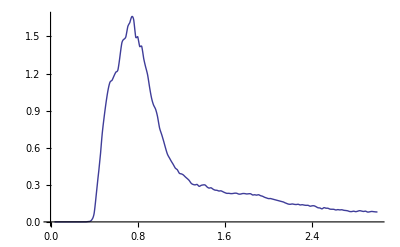

```mathematica
data1=Table[{x*dx,1.55*nv[x,3]},{x,0,nx}];
Interpolation[%];
plot1=Plot[%[x],{x,0,3}]
```

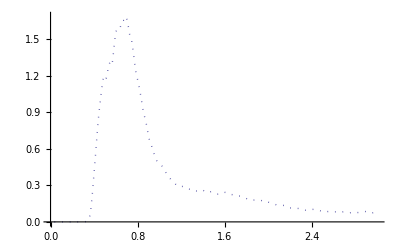

```mathematica
Table[{x*dx,1.55*nv[x,3]},{x,0,nx}];
Interpolation[%];
plot2=Plot[%[x],{x,0,3},PlotStyle->{Directive[Dotted,Thick]}]
```

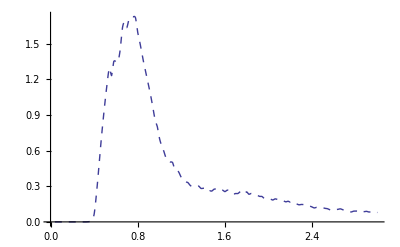

```mathematica
Table[{1.1*x*dx,RandomReal[{0.97,1.03}]* 1.62*nv[x,3]},{x,0,nx}];
Interpolation[%];
plot3=Plot[%[x],{x,0,3},PlotStyle->{Directive[Dashed]}]
```

```mathematica
makePlotLegend[names_,markers_,origin_,markerSize_,fontSize_,font_]:=Join@@Table[{Text[Style[names[[i]],FontSize->fontSize,font],Offset[{1.5*markerSize,-(i-0.5)*Max[markerSize,fontSize]*1.25},Scaled[origin]],{-1,0}],Inset[Show[markers[[i]],ImageSize->markerSize],Offset[{0.5*markerSize,-(i-0.5)*Max[markerSize,fontSize]*1.25},Scaled[origin]],{0,0},Background->Directive[Opacity[0],White]]},{i,1,Length[names]}];
points={{0.5,0.5},{0.65,1.4},{0.8,1.65},{1,1.3}};
GR2=Show[
ListPlot[points,PlotRange->{{0,3},{0,2.2}},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"X^*","C_0"},Ticks->{{1},{1}},Epilog->makePlotLegend[{"my","BB bi-Gaussian", "present bi-Gaussian"},(Graphics[{#,Line[{{-1,0},{1,0}}]}])&/@{Green,Blue,Red},{0.6,0.9},12,12,"Arial"]],
plot1,plot2,plot3
]
NameMovie = exportPictures<>"earth.png";
Export[NameMovie,GR2];
```

-Graphics-

```mathematica
exportPictures
```

/home/igor/Igor/proga/test/data/bb1/pictures/

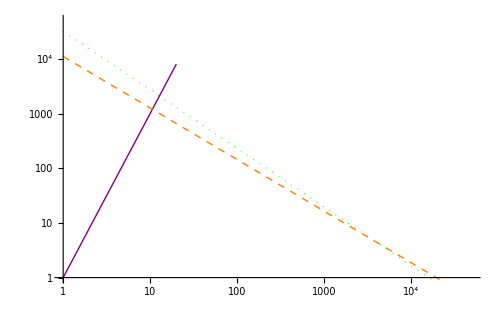

```mathematica
depth4=Range[20]^3;
plot=ListLogLogPlot[Sort[depth4],PlotRange->{{1,50000},{1,50000}},Joined->True,PlotStyle->{Purple},BaseStyle->{FontSize->14}];
line=LogLogPlot[11024 x^(-0.94232),{x,1,100000},PlotStyle->{Orange,Dashed,Thick}];
line2=LogLogPlot[31862 x^(-1.07076),{x,1,100000},PlotStyle->{Green,Dotted,Thick}];

Needs["PlotLegends`"]
ShowLegend[Show[plot,line,line2,ImageSize->500],{{{Graphics[{Purple,Line[{{0,0},{2,0}}]}],"   depth4"},{Graphics[{Orange,Dashed,Line[{{0,0},{2,0}}]}],"   line"},{Graphics[{Green,Dashed,Line[{{0,0},{2,0}}]}],"   line2"}},LegendPosition->{0.7,0.2},LegendSize->{0.45,0.4},LegendShadow->False}]
```

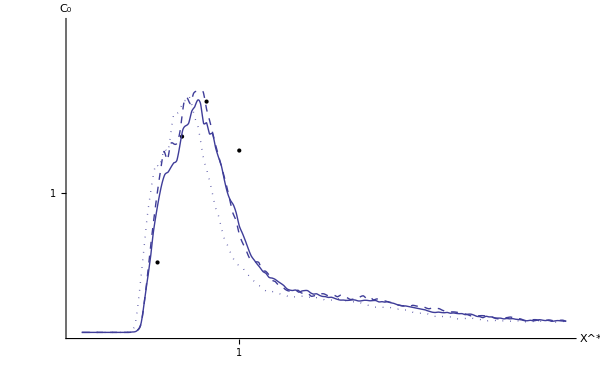

```mathematica
Show[
ListPlot[points,PlotRange->{{0,3},{0,2.2}},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"X^*","C_0"},Ticks->{{1},{1}}],
plot1,plot2,plot3
]
```

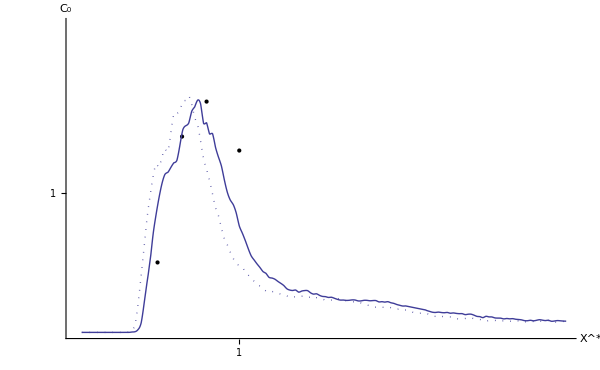

```mathematica
ShowLegend[Show[

plot1,plot2,plot3
ImageSize->600],{{{Graphics[{Line[{{0,0},{2,0}}]}],"   depth4"},{Graphics[{Dotted,Thick,Line[{{0,0},{2,0}}]}],"   line"},{Graphics[{Dashed,Line[{{0,0},{2,0}}]}],"   line2"}},LegendPosition->{0.1,0.2},LegendSize->{0.45,0.4},LegendShadow->False}]
```

```mathematica
simpleLegend[legendItems__,pos_]:=Module[{legendLine,offset,legend},offset=Module[{s,o,insetpts=10},s=pos/.{Left->0,Right->1,Bottom->0,Top->1};
o=insetpts pos/.{Left->1,Right->-1,Bottom->1,Top->-1};
Offset[o,Scaled[s]]];
legendLine[{lbl_,lineStyle_}]:={Graphics[{lineStyle,Line[{{0,0.5},{1,0.5}}]},ImageSize->{20,10},AspectRatio->0.5],Style[lbl,FontFamily->"Tahoma",FontSize->11,TextAlignment->Left,LineBreakWithin->False]};
legend=GraphicsGrid[legendLine/@legendItems,Alignment->Left];
Graphics@Inset[legend,offset,pos]];
```

```mathematica
labels={"data","eq1","eq2"};
styles={Directive[Purple],Directive[Orange,Dashed,Thick],Directive[Green,Dotted,Thick]};

depth4=Table[{x,(11024 x^(-0.94232))*RandomReal[{0.4,1.6}]}/.x->10^n,{n,0,5,0.1}];

plot=ListLogLogPlot[Sort[depth4],PlotRange->{{1,50000},{1,50000}},Joined->True,PlotStyle->styles[[1]],BaseStyle->{FontSize->14}];

line=LogLogPlot[11024 x^(-0.94232),{x,1,100000},PlotStyle->styles[[2]]];
line2=LogLogPlot[31862 x^(-1.07076),{x,1,100000},PlotStyle->styles[[3]]];

Show[plot,line,line2,simpleLegend[Thread@{labels,styles},{Right,Top}]]
```

-Graphics-